### Representative Concentration Pathways - Curate data

```mathematica
(* Import from IPCC *)
data=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/external_data/rcp_trajs.csv"];
```

```mathematica
(* Historical data import up to 2000 *)
historicalEmissionDataRaw=Import["export_data/historical_emissions.dat","Data"]//Transpose;
```

```mathematica
historicalEmissionData=historicalEmissionDataRaw[[1;;-8]];
```

```mathematica
(* from 2000 up to 2100 *)
timeLabels=data[[1,5;;16]];
rcp2p6pre=Transpose[{timeLabels,data[[4,5;;16]]}];
rcp4p5pre=Transpose[{timeLabels,data[[3,5;;16]]}];
rcp6pre=Transpose[{timeLabels,data[[2,5;;16]]}];
rcp8p5pre=Transpose[{timeLabels,data[[5,5;;16]]}];
```

```mathematica
(* rules for extended concentration pathways up to 2300 (taken from Van Vuuren et al. (2011)) *)
rcp2p6post={{2300,-0.42}};
rcp4p5post={{2125,2.5},{2300,1.5}};
rcp6post={{2150,3.25},{2300,1.75}};
rcp8p5post={{2150,28.817},{2250,2.5},{2300,2.5}};
```

```mathematica
rcp2p6=Join[historicalEmissionData,rcp2p6pre,rcp2p6post];
rcp4p5=Join[historicalEmissionData,rcp4p5pre,rcp4p5post];
rcp6=Join[historicalEmissionData,rcp6pre,rcp6post];
rcp8p5=Join[historicalEmissionData,rcp8p5pre,rcp8p5post];
```

```mathematica
legend=LineLegend[TMBcolours[[1;;4]],{"RCP2.6","RCP4.5","RCP6","RCP8.5"},LabelStyle->10]
```

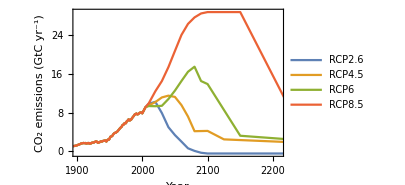

```mathematica
(* plot of rcps *)
rcpPlot=ListLinePlot[{rcp2p6,rcp4p5,rcp6,rcp8p5},PlotRange->{{1900,2210},All},
LabelStyle->12,
Frame->{{True,False},{True,False}},
FrameLabel->{"Year","CO_2 emissions (GtC yr^-1)"},
PlotLegends->Placed[legend,Scaled[{0.15,0.75}]],
ImageSize->300]
```

```mathematica
Export["figures/rcpPlot.png",rcpPlot,ImageResolution->100];
```

```mathematica
(* Export curated data for use in simulations *)
Export["export_data/rcp_data/rcp2p6.dat",rcp2p6];
Export["export_data/rcp_data/rcp4p5.dat",rcp4p5];
Export["export_data/rcp_data/rcp6.dat",rcp6];
Export["export_data/rcp_data/rcp8p5.dat",rcp8p5];
```